# NG^23 T_05. Линейная разделимость, опорные векторы, повышение размерности

5-март-2023
Ковалевская Варвара

## Section. Логический оператор AND как пример линейно разделимых классов

### Section.Subsection. Фазовое пространство

```mathematica
Tuples[{False,True},2]
And@@@%
{X,Y} = {%%,%}/.{False->-1,True->+1}
```

{{False,False},{False,True},{True,False},{True,True}}

{False,False,False,True}

{{{-1,-1},{-1,1},{1,-1},{1,1}},{-1,-1,-1,1}}

```mathematica
Length[iCold=Flatten@Position[Y,-1]]
Length[iWarm=Flatten@Position[Y,+1]]
```

3

1

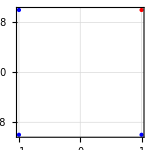

```mathematica
Fig0 = Graphics[{PointSize@Large,Blue,Point@X[[iCold]],Red,Point@X[[iWarm]]},ImageSize->150,Frame->True,PlotRange->2,GridLines->Automatic]
```

### Section.Subsection. Разделительная полоса

```mathematica
ClearAll[SVM];
SVM[W_?VectorQ,w0_]:=W.#-w0&;
SVM[W_?VectorQ]:=W.Flatten@{#,-1}&;
```

```mathematica
SVM[{2,-1},-3]
%@{1,1}
```

{2,-1}.#1--3&

4

```mathematica
SVM[{2,-1,-3}]
%@{1,1}
```

{2,-1,-3}.Flatten[{#1,-1}]&

4

```mathematica
w=RandomReal[{-2,2},3]
```

{-0.683778,0.718239,0.382791}

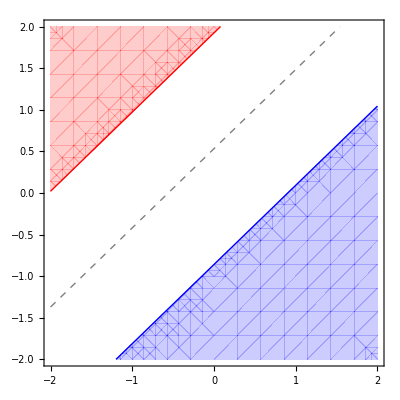

```mathematica
ContourPlot[SVM[w]@{x,y},{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]
```

```mathematica
Dynamic@Show[Fig0,ContourPlot[SVM[w]@{x,y},{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]]
```

## Section. Задача условной оптимизации

```mathematica
#.#&@{w1,w2}
MapThread[#2({w1,w2}.#1-w0)>1&,{X,Y}]
Flatten@{%%,%}
Last@FindMinimum[%,{w1,w2,w0}]
W={w1,w2,w3}/.%
```

w1^2+w2^2

{w0+w1+w2>1,w0+w1-w2>1,w0-w1+w2>1,-w0+w1+w2>1}

{w1^2+w2^2,w0+w1+w2>1,w0+w1-w2>1,w0-w1+w2>1,-w0+w1+w2>1}

{w1→1.,w2→1.,w0→1.}

{1.,1.,w3}

## Section. Логический оператор XOR и повышение размерности фазового пространства

```mathematica
Fig0
```

-Graphics-

```mathematica
ClearAll[Elevate3];
Elevate3[{x1_,x2_}] := {x1,x2, (x1+x2)^2/4}
```

```mathematica
XX = Elevate3/@X
```

{{-1,-1,1},{-1,1,0},{1,-1,0},{1,1,1}}

```mathematica
W = RandomReal[{-2,2},4]
```

{-0.989773,1.11347,-1.95588,1.20885}

```mathematica
Dynamic@Show[Fig0,ContourPlot[SVM[W]@Elevate3@{x,y},{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]]
```

```mathematica
Graphics3D[{PointSize@Large,Blue,Point@XX[[iCold]],Red,Point@XX[[iWarm]]},ImageSize->150,PlotRange->2]
```

-Graphics3D-

```mathematica
ContourPlot3D[SVM[W]@{x,y,z},{x,-2,2},{y,-2,2},{z,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[0.4,Blue],Opacity[0.4,Gray],Opacity[0.4,Red]}, Mesh->False, BoxStyle->None]
```

-Graphics3D-

```mathematica
Dynamic[{Show[Fig0,ContourPlot[SVM[W]@Elevate3@{x,y},{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]],
Show[Graphics3D[{PointSize@Large,Blue,Point@XX[[iCold]],Red,Point@XX[[iWarm]]},ImageSize->150,PlotRange->2],ContourPlot3D[SVM[W]@{x,y,z},{x,-2,2},{y,-2,2},{z,-2,2},Contours->{-1,0,1},ContourStyle->{Opacity[0.4,Blue],Opacity[0.4,Gray],Opacity[0.4,Red]}, Mesh->False, BoxStyle->None]]},TrackedSymbols:>{W}]
```

```mathematica
#.#&@{w1,w2,w3}
MapThread[#2({w1,w2,w3}.#1-w0)>1&,{XX,Y}]
Flatten@{%%,%}
Last@FindMinimum[%,{w1,w2,w3,w0}]
W={w1,w2,w3,w0}/.%
```

w1^2+w2^2+w3^2

{w0+w1+w2-w3>1,w0+w1-w2>1,w0-w1+w2>1,-w0+w1+w2+w3>1}

{w1^2+w2^2+w3^2,w0+w1+w2-w3>1,w0+w1-w2>1,w0-w1+w2>1,-w0+w1+w2+w3>1}

{w1→0.666667,w2→0.666667,w3→0.666667,w0→1.}

{0.666667,0.666667,0.666667,1.}

## Section. Метод опорных векторов

### Section.Subsection. Исходное фазовое пространство

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train = Import["NG23T05Problem.xlsx",{"Sheets","Ковалевская Варвара"}]]
```

{181,3}

```mathematica
Train[[;;3]]
Map[Dimensions,{X=Train[[2;;,{1,2}]], Y = Rationalize@Train[[2;;,3]]}]
```

{{X1,X2,Kind},{1.58694,2.3721,-1.},{-1.09597,2.1065,-1.}}

{{180,2},{180}}

```mathematica
Length[iCold=Flatten@Position[Y,-1]]
Length[iWarm=Flatten@Position[Y,+1]]
%%+%
```

133

47

180

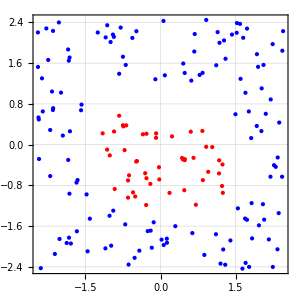

```mathematica
Fig0 = Graphics[{PointSize@Medium,Blue,Point@X[[iCold]],Red,Point@X[[iWarm]]},ImageSize->300,Frame->True,PlotRange->2.7,GridLines->Automatic]
```

### Section.Subsection. Расширенное фазовое пространство

```mathematica
Flatten@Table[x1^(n-i)x2^i,{n,1,4},{i,0,n}]
```

{x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4}

```mathematica
ClearAll[Elevate14];
Elevate14= With[{$ = Flatten@Table[#1^(n-i)#2^i,{n,1,4},{i,0,n}]},$&]
```

{#1,#2,#1^2,#1 #2,#2^2,#1^3,#1^2 #2,#1 #2^2,#2^3,#1^4,#1^3 #2,#1^2 #2^2,#1 #2^3,#2^4}&

```mathematica
Elevate14[3,-1]
```

{3,-1,9,-3,1,27,-9,3,-1,81,-27,9,-3,1}

```mathematica
Dimensions[XX=Elevate14@@@X]
```

{180,14}

### Section.Subsection. Пошаговое выполнение алгоритма SVM

Рис 5. Построение разделительной полосы методом опорных векторов

### Section.Subsection. Разделительная полоса

```mathematica
W
```

{0.666667,0.666667,0.666667,1.}

```mathematica
iS
```

{39,11}

## Section. Опорные точки

```mathematica
ClearAll[SVM];
SVM[W_?VectorQ,w0_]:=W.#-w0&;
SVM[W_?VectorQ]:=W.Flatten@{#,-1}&;
```

```mathematica
Dimensions[Train = Import["NG23T05Problem.xlsx",{"Sheets","Train"}]]
```

{181,3}

```mathematica
Train[[;;3]]
Map[Dimensions,{X=Train[[2;;,{1,2}]], Y = Rationalize@Train[[2;;,3]]}]
```

{{X1,X2,Kind},{1.58694,2.3721,-1.},{-1.09597,2.1065,-1.}}

{{180,2},{180}}

```mathematica
Length[iCold=Flatten@Position[Y,-1]]
Length[iWarm=Flatten@Position[Y,+1]]
%%+%
```

133

47

180

```mathematica
Fig0 = Graphics[{PointSize@Large,Blue,Point@X[[iCold]],Red,Point@X[[iWarm]]},ImageSize->300,Frame->True,PlotRange->2.6,GridLines->Automatic]
```

-Graphics-

```mathematica
Flatten@Table[x1^(n-i)x2^i,{n,1,2},{i,0,n}]
```

{x1,x2,x1^2,x1 x2,x2^2}

```mathematica
ClearAll[Elevate5];
Elevate5= With[{$ = Flatten@Table[#1^(n-i)#2^i,{n,1,2},{i,0,n}]},$&]
```

{#1,#2,#1^2,#1 #2,#2^2}&

```mathematica
Dimensions[XX=Elevate5@@@X]
```

{180,5}

```mathematica
{iS, iC}=TakeDrop[RandomInteger[{1,Length@Y},10],3]
W = RandomReal[{-2,2},6]
```

{{146,65,14},{117,94,52,118,126,132,87}}

{0.27766,0.0571637,0.237152,-1.69675,-0.00254554,0.532329}

```mathematica
CreatePalette@Show[Fig0,
Graphics[{AbsoluteThickness@4,Green,Dynamic[Circle[#,Offset@4]&/@X[[iS]]],Gray,Dynamic[Circle[#,Offset@4]&/@X[[iC]]]}]];
```

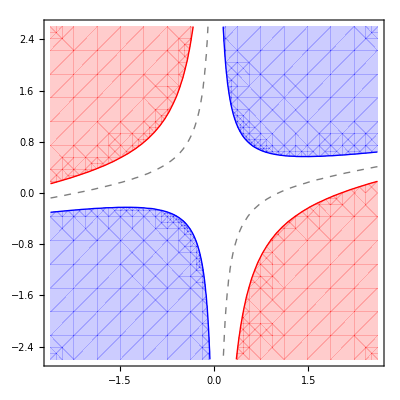

```mathematica
ContourPlot[SVM[W]@Elevate5[x,y],{x,-2.6,2.6},{y,-2.6,2.6},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]
```

```mathematica
CreatePalette[Dynamic[Show[
Fig0,
Graphics[{AbsoluteThickness@4,Green,Circle[#,Offset@4]&/@X[[iS]],Gray,Circle[#,Offset@4]&/@X[[iC]]}],
ContourPlot[SVM[W]@Elevate5[x,y],{x,-2.6,2.6},{y,-2.6,2.6},Contours->{-1,0,1},ContourStyle->{Opacity[1,Blue],Dashed,Opacity[1,Red]},ContourShading->{Opacity[.2,Blue],None,None,Opacity[.2,Red]}]],TrackedSymbols:>{iS,iC,W}],WindowTitle->Dynamic@IntegerString@Length@iS];
```

## Section. Множители Лагранжа и формулировка двойственной задачи

-∑_n λ_n+1/2∑_(n,k) λ_n λ_k y_n y_k OverVector[x_n]·OverVector[x_k]⟶Min
λ_n⩾0
∑_n λ_n y_n==0

```mathematica
iS
Λ = Table[Subscript[λ, n],{n,iS}]
```

{54,61,77,90,99,128,150,168}

{λ_54,λ_61,λ_77,λ_90,λ_99,λ_128,λ_150,λ_168}

```mathematica
Outer[Times,#,#]&@Y[[iS]]
```

{{1,-1,-1,-1},{-1,1,1,1},{-1,1,1,1},{-1,1,1,1}}

```mathematica
XX[[iS]]//Dimensions
Dot[#,#ᵀ]&@XX[[iS]]//Dimensions
```

{4,5}

{4,4}

```mathematica
Dimensions[Q=0.5(Outer[Times,#,#]&@Y[[iS]]) (Dot[#,#ᵀ]&@XX[[iS]])]
```

{8,8}

```mathematica
Q
```

{{0.566139,-0.436264,-1.62555,-0.663927},{-0.436264,20.4487,4.39835,11.5903},{-1.62555,4.39835,13.3002,2.27152},{-0.663927,11.5903,2.27152,16.2636}}

```mathematica
Q.Λ.Λ
```

λ_141 (4.39835 λ_107+13.3002 λ_141+2.27152 λ_179)+λ_107 (20.4487 λ_107+4.39835 λ_141+11.5903 λ_179)+λ_179 (11.5903 λ_107+2.27152 λ_141+16.2636 λ_179)

```mathematica
-Total@Λ+Q.Λ.Λ//Expand
```

-λ_107+20.4487 λ_107^2-λ_141+8.7967 λ_107 λ_141+13.3002 λ_141^2-λ_179+23.1807 λ_107 λ_179+4.54303 λ_141 λ_179+16.2636 λ_179^2

```mathematica
{-Total@Λ+Q.Λ.Λ//Expand,Y[[iS]].Λ==0}
```

{-λ_107+20.4487 λ_107^2-λ_141+8.7967 λ_107 λ_141+13.3002 λ_141^2-λ_179+23.1807 λ_107 λ_179+4.54303 λ_141 λ_179+16.2636 λ_179^2,-λ_107-λ_141-λ_179==0}

```mathematica
Thread[-10<Λ]
```

{-10<λ_7,-10<λ_107,-10<λ_141,-10<λ_179}

```mathematica
solΛ=FindArgMin[{-Total@Λ+Q.Λ.Λ//Expand,Y[[iS]].Λ==0,Sequence@@Thread[-10<Λ]},Λ]
```

{10.5717,-1.34573,16.3379,-10.,11.0328,9.61726,-8.5275,-10.}

```mathematica
Y[[iS]]  solΛ
```

{-10.5717,1.34573,16.3379,10.,11.0328,-9.61726,-8.5275,-10.}

## Section. Последовательный метод активных ограничений

### Section.Subsection. Инициализация множества опорных точек

```mathematica
iS={sCold=RandomChoice@iCold}
```

{148}

```mathematica
sWarm = iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]
```

146

```mathematica
iS=Union[iS,{sWarm }]
```

{146,148}

```mathematica
iS={sCold=iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]],sWarm}
```

{73,146}

```mathematica
4;
iS=Union@@Table[FixedPoint[(iS={sCold,sWarm=iWarm[[First@Nearest[XX[[iWarm]]->"Index",XX[[sCold]]]]]};
iS={sCold=iCold[[First@Nearest[XX[[iCold]]->"Index",XX[[sWarm]]]]],sWarm})&,
iS={sCold=RandomChoice@iCold}],
{%}]
```

{54,61,77,90,99,128,150,168}

### Section.Subsection. Построение разделительной полосы

W⃗==∑_i λ_i Y_i OverVector[XX_i],   w_0==Median{W⃗·OverVector[XX_i]-Y_i|0<λ_i}_i

```mathematica
W1=Dot[Y[[iS]] solΛ,XX[[iS]]]
```

{0.35425,-0.794206,-1.41458,-0.323994,-2.10326}

```mathematica
W0=Median[XX[[iS]].W1-Y[[iS]]]
```

-3.49798

```mathematica
W = Flatten@{W1,W0}
```

{0.35425,-0.794206,-1.41458,-0.323994,-2.10326,-3.49798}

### Section.Subsection. Проверка опорных точек

```mathematica
solΛ
```

{10.5717,-1.34573,16.3379,-10.,11.0328,9.61726,-8.5275,-10.}

```mathematica
pos=Position[#,Min@#,1,1]&@solΛ
iC=Extract[iS,%]
```

{{4}}

{90}

### Section.Subsection. Ложная опорная точка

```mathematica
{iS=DeleteCases[iS,pos],iC={}}
```

{{54,61,77,90,99,128,150,168},{}}

### Section.Subsection. Отступы

```mathematica
Length[iO = Complement[Range@Length@Y,iS]]
```

172

```mathematica
Length[M=MapThread[#2 SVM[W]@#1&,{XX[[iO]],Y[[iO]]}]]
```

172

```mathematica
Min@M
```

0.325469

```mathematica
iC=Extract[iO,Position[M,Min@M,1,1]]
```

{64}

### Section.Subsection. Новая опорная точка

```mathematica
iS=Union[iS,iC]
iC = {}
```

{54,61,64,77,90,99,128,150,168}

{}

### Section.Subsection. Конец алгоритма